```mathematica
π^2/2.
```

4.9348

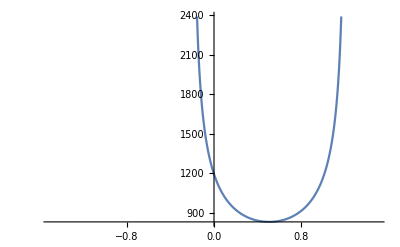

```mathematica
Block[{t=0.3530,a=0.0017,μ=0.2},Plot[1/(2t*a √(((μ+E)/t)-((μ+E)/(2t))^2))+1/(2t*a √(((μ+E)/t)-((μ+E)/(2t))^2)),{E,-1.5,1.5}]]
```

```mathematica
KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]//MatrixForm
```

(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)

```mathematica
ϵk*KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]+Δ*KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]//MatrixForm
```

(ϵk | 0 | 0 | -Δ
0 | ϵk | Δ | 0
0 | Δ | -ϵk | 0
-Δ | 0 | 0 | -ϵk)

```mathematica
Eigensystem[ϵk*KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]+Δ*KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]]
```

{{-√(Δ^2+ϵk^2),-√(Δ^2+ϵk^2),√(Δ^2+ϵk^2),√(Δ^2+ϵk^2)},{{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1},{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0},{-(ϵk+√(Δ^2+ϵk^2))/Δ,0,0,1},{0,-(-ϵk-√(Δ^2+ϵk^2))/Δ,1,0}}}

```mathematica
ϵk*KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]+Δ*KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]+B*KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]//MatrixForm
```

(B+ϵk | 0 | 0 | -Δ
0 | -B+ϵk | Δ | 0
0 | Δ | -B-ϵk | 0
-Δ | 0 | 0 | B-ϵk)

```mathematica
Eigensystem[ϵk*KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]+Δ*KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]+B*KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]]
```

{{-B-√(Δ^2+ϵk^2),B-√(Δ^2+ϵk^2),-B+√(Δ^2+ϵk^2),B+√(Δ^2+ϵk^2)},{{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0},{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1},{0,-(-ϵk-√(Δ^2+ϵk^2))/Δ,1,0},{-(ϵk+√(Δ^2+ϵk^2))/Δ,0,0,1}}}

```mathematica
{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}.SparseArray[{{3,2}->-1,{4,1}->1},{4,4}].{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}/{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}.{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}//FullSimplify
```

Δ/(2 √(Δ^2+ϵk^2))

```mathematica
{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1}.SparseArray[{{3,2}->-1,{4,1}->1},{4,4}].{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1}/{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1}.{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1}//FullSimplify
```

Δ/(2 √(Δ^2+ϵk^2))

```mathematica
{0,-(-ϵk-√(Δ^2+ϵk^2))/Δ,1,0}.SparseArray[{{3,2}->-1,{4,1}->1},{4,4}].{0,-(-ϵk-√(Δ^2+ϵk^2))/Δ,1,0}
```

(-ϵk-√(Δ^2+ϵk^2))/Δ

```mathematica
{-(ϵk+√(Δ^2+ϵk^2))/Δ,0,0,1}.SparseArray[{{3,2}->-1,{4,1}->1},{4,4}].{-(ϵk+√(Δ^2+ϵk^2))/Δ,0,0,1}
```

-(ϵk+√(Δ^2+ϵk^2))/Δ

```mathematica
{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}.{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}
```

1+((-ϵk+√(Δ^2+ϵk^2))^2)/Δ^2

```mathematica
Block[{Δ=1.008,t=0.353,μ=2,g=3},1/2 g*Δ/(2π)*NIntegrate[1/(√(Δ^2+(t*ϕ^2-μ)^2)),{ϕ,-π,π}]]
```

1.00796

```mathematica
Block[{Δ=0.8937,t=0.353,μ=2,g=3},1/2 g*Δ/(2π)*NIntegrate[1/(√(Δ^2+(2*t*(1-Cos[ϕ])-μ)^2)),{ϕ,-π,π}]]
```

0.893728

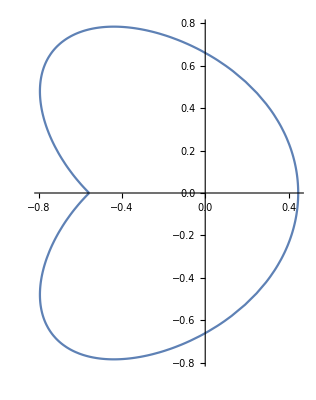

```mathematica
Block[{Δ=1.008,t=0.353,μ=2,g=3},PolarPlot[1/(√(Δ^2+(t*ϕ^2-μ)^2)),{ϕ,-π,π}]]
```

```mathematica
(Integrate[1/(√(Δ^2+(t*ϕ^2-μ)^2)),ϕ]/.ϕ->π)-(Integrate[1/(√(Δ^2+(t*ϕ^2-μ)^2)),ϕ]/.ϕ->-π)//Simplify
```

-(2 ⅈ √(1+(ⅈ π^2 t)/(Δ-ⅈ μ)) √(1-(ⅈ π^2 t)/(Δ+ⅈ μ)) EllipticF[ⅈ ArcSinh[π √(-(ⅈ t)/(Δ+ⅈ μ))],-(Δ+ⅈ μ)/(Δ-ⅈ μ)])/(√(-(ⅈ t)/(Δ+ⅈ μ)) √(Δ^2+(-π^2 t+μ)^2))

```mathematica
Reduce[-(2 ⅈ √(1+(ⅈ π^2 t)/(Δ-ⅈ μ)) √(1-(ⅈ π^2 t)/(Δ+ⅈ μ)) EllipticF[ⅈ ArcSinh[π √(-(ⅈ t)/(Δ+ⅈ μ))],-(Δ+ⅈ μ)/(Δ-ⅈ μ)])/(√(-(ⅈ t)/(Δ+ⅈ μ)) √(Δ^2+(-π^2 t+μ)^2))==4π/g,Δ]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[-(2 ⅈ √(1+(ⅈ π^2 t)/(Δ-ⅈ μ)) √(1-(ⅈ π^2 t)/(Δ+ⅈ μ)) EllipticF[ⅈ ArcSinh[π √(-(ⅈ t)/(Δ+ⅈ μ))],-(Δ+ⅈ μ)/(Δ-ⅈ μ)])/(√(-(ⅈ t)/(Δ+ⅈ μ)) √(Δ^2+(-π^2 t+μ)^2))==(4 π)/g,Δ]

```mathematica
Solve[(Integrate[1/(√(Δ^2+(t*ϕ^2-μ)^2)),ϕ]/.ϕ->π)-(Integrate[1/(√(Δ^2+(t*ϕ^2-μ)^2)),ϕ]/.ϕ->-π)==4π/g,Δ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(2 ⅈ √(1+(ⅈ π^2 t)/(Δ-ⅈ μ)) √(1-(ⅈ π^2 t)/(Δ+ⅈ μ)) EllipticF[ⅈ ArcSinh[π √(-(ⅈ t)/(Δ+ⅈ μ))],-(Δ+ⅈ μ)/(Δ-ⅈ μ)])/(√(-(ⅈ t)/(Δ+ⅈ μ)) √(Δ^2+(-π^2 t+μ)^2))==(4 π)/g,Δ]

```mathematica
(ArcTanh[(k √x)/(√(k^2 x+Δ^2-μ))]/(√x)/.k->u)-(ArcTanh[(k √x)/(√(k^2 x+Δ^2-μ))]/(√x)/.k->-u)
```

(2 ArcTanh[(u √x)/(√(u^2 x+Δ^2-μ))])/(√x)